IGraph/M 0.3.108 (December 17, 2018)

Evaluate IGDocumentation[] to get started.

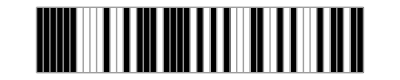

```mathematica
<<IGraphM`
ClearAll[graph];
Nn=(7)^2;(*number of spins*)mcs=100;(*Monte Carlo steps*)J=1;(*interaction strength*)
graph = IGSquareLattice[{Sqrt[Nn],Sqrt[Nn]}];
myA =AdjacencyMatrix[graph];
b=0; 
kT=Range[4,1,-0.2];(*range of temperatures*)NkT=Length[kT];
bσ=RandomChoice[{1,-1},Nn];(*random initial state*)
h=0;
myH[σ_,myA_]:= For[k=1,k<=Nn,k++,
				h = h - b*σ[[k]]; 
				For[j=1, j < k,j++,
				h = -2*J*σ[[j]]*myA[[k]][[j]] + h;];
				   ];
myHFlip[σ_,myA_,iterM_]:=Function[
				h = h - 2*b*σ[[iterM]]; 
				For[j=1, j < iterM,j++,
				h = -2*2*J*σ[[j]]*myA[[iterM]][[j]] + h;];]
bσ = {1,1,1,1,1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,1,1,1,1,-1,1,-1,1,-1,1,-1,-1,-1,1,1,-1,-1,1,-1,1,-1,-1,-1,1,-1,1,1,-1,1,1};
(* simmetry and deltaH*)
myH[bσ,myA];
hOld = h;
h = 0;
(* step iniziale per la h *)
time = Table[Table[0,{jj,1,Nn}],{j,1,mcs+1}];
time[[1]]=Table[bσ[[jj]],{jj,1,Nn}];
ArrayPlot[{1/2 (bσ+1)},Mesh->All]
```

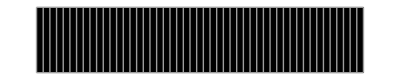
{24.956,-Graphics-}

```mathematica
Timing[
iT = NkT;
β=1/kT[[iT]];(*β=1/kT*)
For[kk=2,kk≤mcs+1,kk++,
(*Monitor[*)
For[t=1,t≤Nn,t++,
(*loop over Monte Carlo steps*)(*choose the spin to flip*)
xflip=RandomInteger[{1,Nn}];
(*acceptance step*)
flipped = bσ;
flipped[[xflip]] = -flipped[[xflip]] ;
myH[flipped,myA];
deltaH = (h - hOld);
(*majority*)
(*α=Min[1,1/(1+Exp[2*β deltaH])];*)
α = Min[1,Exp[-β deltaH]];
u=RandomReal[{0,1}];
If[u≤α,tt=bσ[[xflip]];
hOld = h;
h = 0;
bσ[[xflip]]=-tt,h = 0;
];(*end For i*)(*calculate<M>and<M^2>*)
(*plot=ArrayPlot[{1/2 (bσ+1)},Mesh->All];*)];
(*,plot];*)
(*Print["End of the ",kk," mcs iteration"];*)
time[[kk]]=Table[bσ[[jj]],{jj,1,Nn}];];
ArrayPlot[{1/2 (bσ+1)},Mesh->All]]
```

```mathematica
ArrayPlot[1/2 (Transpose[time]+1),Mesh->All]
```

-Graphics-

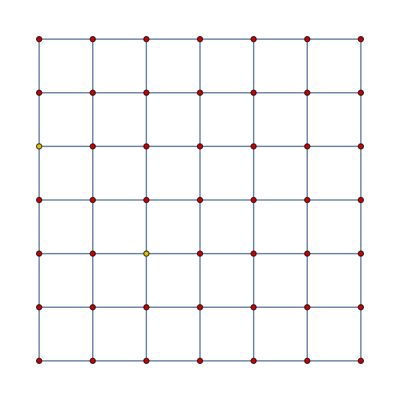

```mathematica
vettW = Table[0,{mj,1,Nn}];
vettB = Table[0,{j,1,Nn}];
k=0; j = 1; l = 1;
For[k=1,k <= Nn,k++,
If[bσ[[k]] == 1,vettW[[j]]=k; j++,vettB[[l]]=k;l++]]
HighlightGraph[graph,{vettW,vettB}]
ArrayPlot[{1/2 (bσ+1)},Mesh->All] (* okay, visualizza da sx verso alto, prima colonna, poi seconda colonna e così via*}
```

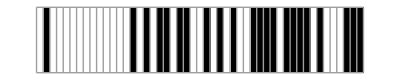
{0.896,-Graphics-}

```mathematica
Timing[
iT = NkT;
β=1/kT[[iT]];(*β=1/kT*)
For[kk=2,kk≤mcs+1,kk++,
(*Monitor[*)
For[t=1,t≤Nn,t++,
(*loop over Monte Carlo steps*)(*choose the spin to flip*)
xflip=RandomInteger[{1,Nn}];
h=0;
h = h - 2*b*bσ[[xflip]];
	For[j=1, j < xflip,j++,
	h = -2*2*J*bσ[[j]]*myA[[xflip]][[j]] + h;];
deltaH = h ;
(*α=Min[1,1/(1+Exp[2*β deltaH])];*)
α = Min[1,Exp[-β deltaH]];
u=RandomReal[{0,1}];
If[u≤α,tt=bσ[[xflip]];
bσ[[xflip]]=-tt,bσ[[xflip]]=tt;
];(*end For i*)(*calculate<M>and<M^2>*)
(*plot=ArrayPlot[{1/2 (bσ+1)},Mesh->All];*)];
(*,plot];*)
(*Print["End of the ",kk," mcs iteration"];*)
time[[kk]]=Table[bσ[[jj]],{jj,1,Nn}];];
ArrayPlot[{1/2 (bσ+1)},Mesh->All]]
```

```mathematica
h=0;
myHFlip[bσ,myA,xflip];
h
flipped
```

-10

{1,1,1,-1,1,1,-1,-1,-1,1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,1,1,1,1,1,1,-1,-1,1,1,1,-1,1,1,-1,1,1,-1,1,1,1,-1,-1,-1,-1,1,1,-1}

```mathematica
bσ = {1,1,1,1,1,1,-1,-1,-1,-1,1,-1,-1,1,-1,1,1,1,-1,1,1,1,1,-1,1,-1,1,-1,1,-1,-1,-1,1,1,-1,-1,1,-1,1,-1,-1,-1,1,-1,1,1,-1,1,1};
```